# Les valeurs propres et les vecteurs propres de l’opérateurs Hermitien (Opérateur différentiel)

## Définitions

### Fonction poid

```mathematica
w:=ⅇ^(-x^2)
```

### Intervalle d’orthogonalité

```mathematica
a:=-∞
```

```mathematica
b:=∞
```

### Produit scalaire

```mathematica
⟨u_|v_⟩:=∫_a^b w u vⅆx
```

### Norme

```mathematica
norm[x_]:=√⟨x|x⟩
```

### Normalization

```mathematica
normalize[x_]:=x/(√⟨x|x⟩)
```

### Orthogonalization

```mathematica
orthogonalize[x_]:=Orthogonalize[x,⟨#1|#2⟩&]
```

### verification

```mathematica
verification[x_]:=MatrixForm[Outer[⟨#1|#2⟩&,x,x]]
```

### Projection orthogonale

```mathematica
projection[y_,x_]:=⟨x|y⟩x/⟨x|x⟩
```

## Exemple

### Base Quelconque

```mathematica
u=Table[x^n,{n,0,3}]
```

{1,x,x^2,x^3}

### Orthogonalisation

```mathematica
ϕ=orthogonalize[u]
```

{1/π^(1/4),(√2 x)/π^(1/4),(√2 (-1/2+x^2))/π^(1/4),(2 (-(3 x)/2+x^3))/(√3 π^(1/4))}

### Vérification

```mathematica
verification[ϕ]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

### La fonction à développer

```mathematica
ψ :=Sin[x]
```

### Les coéfficients de Fourier

```mathematica
c=⟨ϕ|ψ⟩
```

{0,(π/ⅇ)^(1/4)/(√2),0,-(π/ⅇ)^(1/4)/(4 √3)}

### Les projections

```mathematica
c ϕ
```

{0,x/ⅇ^(1/4),0,-(-(3 x)/2+x^3)/(6 ⅇ^(1/4))}

### Dévelopement de ψ(x) sur la base orthonormale

```mathematica
development=Sum[k,{k,c ϕ}]
```

x/ⅇ^(1/4)-(-(3 x)/2+x^3)/(6 ⅇ^(1/4))

### Représentation

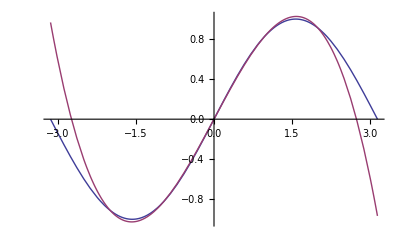

```mathematica
Plot[Evaluate[{ψ,development}],{x,-π,π},PlotRange->All]
```

```mathematica
P=Abs[c]^2
```

{0,(√(π/ⅇ))/2,0,(√(π/ⅇ))/48}